```mathematica
loadNotebook["uproszczony_off_9_model.nb"];
loadNotebook["inz_off_model_psi.nb"];
```

```mathematica
wyrysuj[rozwiazanie_, tmax_,anim_]:=Module[{},
Plot[xd[t]-x[t]/.rozwiazanie,{t,0,tmax},AxesLabel->{"t","ex"}]// Print;
Plot[yd[t]-y[t]/.rozwiazanie,{t,0,tmax},AxesLabel->{"t","ey"}] // Print;Plot[Evaluate[{Subscript[ϕ, 1][t], Subscript[ϕ, 2][t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ϕ"}, PlotLegends->{"ϕ_1","ϕ_2"},Axes->{True, True}]// Print;
Plot[Evaluate[{Subscript[θ, 1][t],  Subscript[θ, 2][t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","θ"}, PlotLegends->{"θ_1","θ_2"},Axes->{True, True}]// Print;
Plot[Evaluate[{Subscript[ψ, 1]'[t], Subscript[ψ, 2]'[t]} /.rozwiazanie], {t,0,tmax}, PlotRange->All, AxesLabel->{"t","ψ̇"}, PlotLegends->{"(ψ̇)_1","(ψ̇)_2"},Axes->{True, True}]// Print;
krzywa1[t_] = {x[t] ,y[t]} /. rozwiazanie;

p1[t_] = ((Agms[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x1[t_] = (p1[t])[[1,1,1]];
y1[t_] = (p1[t])[[1,2,1]];
krzywas[t_] = {x1[t], y1[t]} /. rozwiazanie;

p2[t_] = ((Agm2[x[t], y[t], Subscript[θ, 0][t]]/.rozwiazanie).Transpose[{{0,0,0,1}}]) /. {l-> 0.1, R-> 0.03};
x2[t_] = (p2[t])[[1,1, 1]];
y2[t_] = (p2[t])[[1,2, 1]];
krzywa2[t_] = {x2[t], y2[t]}/. rozwiazanie;

ẋ[t_] = (x1'[t] /.rozwiazanie)[[1]];
ẏ[t_] = (y1'[t] /. rozwiazanie)[[1]];
v[t_] = Re[Sqrt[(ẋ[t])^2+(ẏ[t])^2]];

krzywad[t_]={xd[t],yd[t]};

a1 = Animate[
Show[
{Plot[v[t], {t, 0, tmax}, PlotRange->All,AxesLabel->{"t","v"}]},
{
Graphics[{PointSize[Large],Red,Point[Dynamic[{t,v[t]}]]}]
}
],{t,0,tmax}];

curvs = ParametricPlot[{krzywas[t]}, {t, 0, tmax}, PlotRange->All, PlotStyle->{Red}, Axes->{True, True}, AxesOrigin->{0,0}];
curv1 = ParametricPlot[{krzywa1[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Blue}, Axes->{True, True},AxesOrigin->{0,0}];
curv2 = ParametricPlot[{krzywa2[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Yellow}, Axes->{True, True}, AxesOrigin->{0,0}];
curvd = ParametricPlot[{krzywad[t]}, {t, 0, tmax}, PlotRange->All,PlotStyle->{Black}, Axes->{True, True}, AxesOrigin->{0,0}];
ParametricPlot[{krzywa1[t],krzywad[t]},{t, 0, tmax},PlotRange->All,PlotStyle->{Red,Black}, Axes->{True, True}, AxesOrigin->{0,0}] // Print;


p11[t_]=Evaluate[{x[t],y[t]}/.rozwiazanie];
p22[t_]=Evaluate[{x2[t],y2[t]}/.rozwiazanie];
x11[t_]=(x[t]/.rozwiazanie)[[1]];
y11[t_]=(y[t]/.rozwiazanie)[[1]];
x22[t_]=(x2[t]/.rozwiazanie)[[1]];
y22[t_]=(y2[t]/.rozwiazanie)[[1]];
a2=Animate[
Show[
{curvs,curv1,curv2,curvd},
{
Graphics[{PointSize[0.03],Red,Point[Dynamic[p11[t]]]}],
Graphics[{PointSize[0.03], Red,Point[Dynamic[p22[t]]]}],
Graphics[{PointSize[0.02], Black,Point[Dynamic[{xd[t],yd[t]}]]}],
Graphics[
{Thickness[0.002],Green,
Line[
{
Dynamic[{x11[t],y11[t]}],
Dynamic[{x2[t],y2[t]}]
}
]
}]
}
],{t,0,tmax}];
If[anim,Print[a1],0];
If[anim,Print[a2],0];
0
];
```

```mathematica
wyliczSterowanie[wd_,w_,k1_]:=(
M= Inverse[D[w,{qu[t]}].G2u ];
Det[D[w,{qu[t]}].G2u ] // Simplify // Print;
K1=k1*IdentityMatrix[5];
M=M.(D[wd,t]-K1.(w-wd));
M=Insert[M,M[[2]]*Sin[Subscript[θ, u1][t]]/Sin[Subscript[θ, u2][t]],4];
M=M/.{Subscript[ϕ, u1][t]->Subscript[ψ, 1][t],Subscript[ϕ, u2][t]->Subscript[ψ, 2][t],Subscript[r, 1][t]->R*Sqrt[((Cos[Subscript[ϕ, 1][t]])^2)(Sin[Subscript[θ, 1][t]]^2 )+(Sin[Subscript[ϕ, 1][t]]^2 )],Subscript[r, 2][t]->R*Sqrt[((Cos[Subscript[ϕ, 2][t]])^2)(Sin[Subscript[θ, 2][t]]^2 )+(Sin[Subscript[ϕ, 2][t]]^2 )]};
M=M/.{Subscript[θ, u1][t]->ArcTan[Sin[Subscript[θ, 1][t]]/(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]])],Subscript[θ, u2][t]->ArcTan[Sin[Subscript[θ, 2][t]]/(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]])]};
M=M /.{l-> 0.1, R-> 0.03};
M
);
```

-0.05 r_1

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

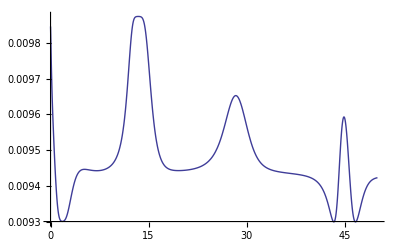

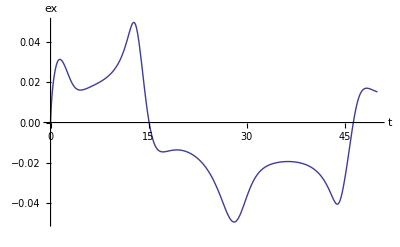

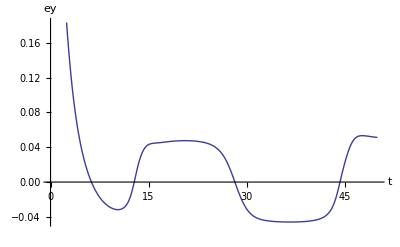

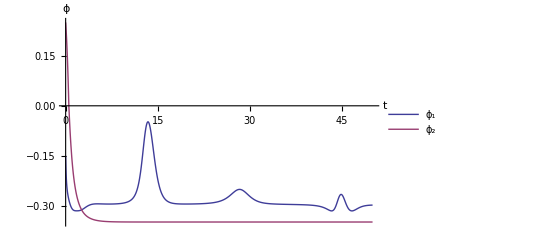

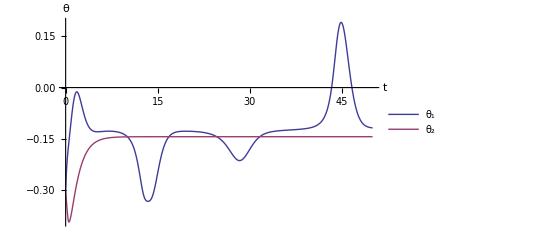

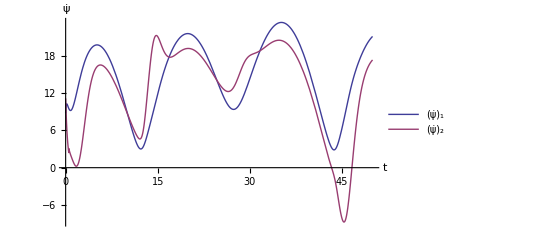

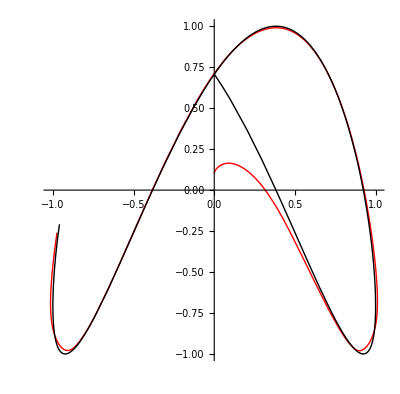

0

```mathematica
{xd[t_],yd[t_]}=osemka[t,5];
td[t_]=0.4;
d = 0.05;
w={x[t]+d*Cos[Subscript[θ, u1][t]+Subscript[θ, 0][t]],y[t]+d*Sin[Subscript[θ, u1][t]+Subscript[θ, 0][t]],Subscript[θ, u2][t]};
wd={xd[t],yd[t],td[t]};
M =wyliczSterowanie[wd,w,0.4];

w1 = Solve[{0.02==0.03*Sqrt[((Cos[Subscript[ϕ, 1][t]])^2)(Sin[Subscript[θ, 1][t]]^2 )+(Sin[Subscript[ϕ, 1][t]]^2 )],  Tan[Subscript[θ, u1][t]] ==(Sin[Subscript[θ, 1][t]])/(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]])}, {Subscript[ϕ, 1][t],Subscript[θ, 1][t]}];w2 = Solve[{0.02==0.03*Sqrt[((Cos[Subscript[ϕ, 2][t]])^2)(Sin[Subscript[θ, 2][t]]^2 )+(Sin[Subscript[ϕ, 2][t]]^2 )],  Tan[Subscript[θ, u2][t]] ==(Sin[Subscript[θ, 2][t]])/(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]])}, {Subscript[ϕ, 2][t],Subscript[θ, 2][t]}];
ster={Subscript[ϕ, 1][t],Subscript[θ, 1][t],Subscript[ψ, 1][t], Subscript[ϕ, 2][t], Subscript[θ, 2][t],Subscript[ψ, 2][t]};
ster = ster /.{Subscript[ϕ, 1][t]->-1. ArcCos[trim[(√(5.+5. Tan[Subscript[θ, u1][t]]^2))/(√(9.+5. Tan[Subscript[θ, u1][t]]^2)),-1, 1]],Subscript[θ, 1][t]->-1. ArcSin[trim[(2. Tan[Subscript[θ, u1][t]])/(√(9.+9. Tan[Subscript[θ, u1][t]]^2)),-1, 1]]};
ster = ster /.{Subscript[ϕ, 2][t]->-1. ArcCos[trim[(√(5.+5. Tan[Subscript[θ, u2][t]]^2))/(√(9.+5. Tan[Subscript[θ, u2][t]]^2)),-1,1]],Subscript[θ, 2][t]->-1. ArcSin[trim[(2. Tan[Subscript[θ, u2][t]])/(√(9.+9. Tan[Subscript[θ, u2][t]]^2)),-1,1]]};
(*ster=ster/.w2[[5]];*)
ster = ster /.{Subscript[ψ, 1][t]->Subscript[ϕ, u1][t],Subscript[ψ, 2][t]->Subscript[ϕ, u2][t]};
ster // MatrixForm;
ster=D[ster,t];
ster=ster/.{Subscript[ϕ, u1][t]->Subscript[ψ, 1][t],Subscript[ϕ, u2][t]->Subscript[ψ, 2][t],Subscript[r, 1]->R*Sqrt[((Cos[Subscript[ϕ, 1][t]])^2)(Sin[Subscript[θ, 1][t]]^2 )+(Sin[Subscript[ϕ, 1][t]]^2 )],Subscript[r, 2]->R*Sqrt[((Cos[Subscript[ϕ, 2][t]])^2)(Sin[Subscript[θ, 2][t]]^2 )+(Sin[Subscript[ϕ, 2][t]]^2 )]};
ster=ster/.{Subscript[θ, u1][t]->ArcTan[Sin[Subscript[θ, 1][t]]/(Cos[Subscript[θ, 1][t]]Sin[Subscript[ϕ, 1][t]])],Subscript[θ, u2][t]->ArcTan[Sin[Subscript[θ, 2][t]]/(Cos[Subscript[θ, 2][t]]Sin[Subscript[ϕ, 2][t]])]};
ster=ster/.{D[Subscript[θ, u1][t],t]->M[[1]],D[Subscript[ϕ, u1][t],t]->M[[2]],D[Subscript[θ, u2][t],t]->M[[3]],D[Subscript[ϕ, u2][t],t]->M[[4]]};
ster //MatrixForm;

q0={x[0]== 0, y[0]==0.1, Subscript[θ, 0][0]==0.4, Subscript[ϕ, 1][0]==-0.15, Subscript[θ, 1][0]== -0.3, Subscript[ψ, 1][0]==0,Subscript[ϕ, 2][0]== 0.25, Subscript[θ, 2][0]==-0.3, Subscript[ψ, 2][0]==0};

tmax =50;
pstrona = Transpose[G2.Transpose[{η[t]}]][[1]];
lstrona = D[q[t],t];
rownanie = Apply[Equal, Transpose[{lstrona, pstrona}],1];
tosolve = (rownanie /.{Subscript[η, 1][t] -> ster[[1]], Subscript[η, 2][t]->ster[[2]],Subscript[η, 3][t]->ster[[3]],Subscript[η, 4][t]->ster[[4]],Subscript[η, 5][t]->ster[[5]], l-> 0.1, R-> 0.03}) ~Join~ q0;
roz = NDSolve[tosolve, {x,y, Subscript[θ, 0],Subscript[ϕ, 1], Subscript[θ, 1],Subscript[ψ, 1], Subscript[ϕ, 2], Subscript[θ, 2],Subscript[ψ, 2]}, {t,0,tmax}, Method->Automatic, MaxSteps->1000000];
Plot[0.03*Sqrt[((Cos[Subscript[ϕ, 1][t]])^2)(Sin[Subscript[θ, 1][t]]^2 )+(Sin[Subscript[ϕ, 1][t]]^2 )]/.roz,{t,0,tmax}]
wyrysuj[roz,tmax, True]
```